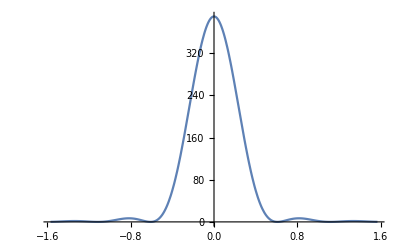

```mathematica
Plot[(Integrate[(x BesselJ[0, r x]), {x, 0, 2 Pi}])^2, {r, -Pi/2, Pi/2}]
```

```mathematica
f[x_, r_] =  (x BesselJ[0, r x])
```

x BesselJ[0,r x]

```mathematica
Plot[(Integrate[f[x, r], {x, 0, 2 Pi}])^2, {r, -Pi/2, Pi/2}]
```

-Graphics-

```mathematica
fintegral[r_] = (Integrate[f[x, r], {x, 0, 2 Pi}])^2
```

(4 π^2 BesselJ[1,2 π r]^2)/r^2

```mathematica
Plot[fintegral[r], {r, -Pi/2, Pi/2}]
```

-Graphics-

```mathematica
Table[{N[r, 10], N[fintegral[r], 10]}, {r, -Pi/2 , Pi/2, Pi/1000}] // TableForm
```

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression 0 π^2 ComplexInfinity encountered.

-1.570796327 | 0.09208598322
-1.567654734 | 0.1046352423
-1.564513141 | 0.11798194
-1.561371549 | 0.1321198569
-1.558229956 | 0.1470415256
-1.555088364 | 0.1627382276
-1.551946771 | 0.1791999914
-1.548805178 | 0.1964155928
-1.545663586 | 0.2143725571
-1.542521993 | 0.2330571631
-1.5393804 | 0.2524544489
-1.536238808 | 0.2725482197
-1.533097215 | 0.2933210576
-1.529955622 | 0.3147543331
-1.52681403 | 0.3368282188
-1.523672437 | 0.3595217048
-1.520530844 | 0.3828126163
-1.517389252 | 0.4066776329
-1.514247659 | 0.4310923098
-1.511106066 | 0.4560311012
-1.507964474 | 0.4814673854
-1.504822881 | 0.5073734918
-1.501681288 | 0.5337207301
-1.498539696 | 0.5604794206
-1.495398103 | 0.5876189273
-1.49225651 | 0.6151076922
-1.489114918 | 0.6429132716
-1.485973325 | 0.6710023738
-1.482831732 | 0.6993408992
-1.47969014 | 0.7278939817
-1.476548547 | 0.7566260315
-1.473406955 | 0.7855007801
-1.470265362 | 0.8144813265
-1.467123769 | 0.8435301842
-1.463982177 | 0.8726093321
-1.460840584 | 0.9016802633
-1.457698991 | 0.9307040384
-1.454557399 | 0.9596413381
-1.451415806 | 0.988452518
-1.448274213 | 1.017097664
-1.445132621 | 1.045536651
-1.441991028 | 1.073729196
-1.438849435 | 1.101634923
-1.435707843 | 1.129213419
-1.43256625 | 1.156424296
-1.429424657 | 1.183227249
-1.426283065 | 1.209582126
-1.423141472 | 1.23544898
-1.419999879 | 1.26078814
-1.416858287 | 1.285560274
-1.413716694 | 1.309726446
-1.410575101 | 1.33324819
-1.407433509 | 1.356087567
-1.404291916 | 1.378207231
-1.401150324 | 1.399570496
-1.398008731 | 1.420141397
-1.394867138 | 1.439884756
-1.391725546 | 1.458766246
-1.388583953 | 1.476752451
-1.38544236 | 1.493810935
-1.382300768 | 1.509910298
-1.379159175 | 1.525020242
-1.376017582 | 1.539111629
-1.37287599 | 1.552156545
-1.369734397 | 1.564128355
-1.366592804 | 1.575001761
-1.363451212 | 1.584752862
-1.360309619 | 1.593359209
-1.357168026 | 1.600799855
-1.354026434 | 1.607055416
-1.350884841 | 1.612108112
-1.347743248 | 1.615941825
-1.344601656 | 1.618542144
-1.341460063 | 1.619896411
-1.33831847 | 1.619993764
-1.335176878 | 1.618825183
-1.332035285 | 1.616383526
-1.328893692 | 1.61266357
-1.3257521 | 1.607662044
-1.322610507 | 1.601377668
-1.319468915 | 1.593811177
-1.316327322 | 1.584965354
-1.313185729 | 1.574845055
-1.310044137 | 1.563457235
-1.306902544 | 1.550810963
-1.303760951 | 1.536917446
-1.300619359 | 1.52179004
-1.297477766 | 1.505444265
-1.294336173 | 1.487897816
-1.291194581 | 1.469170563
-1.288052988 | 1.449284561
-1.284911395 | 1.428264049
-1.281769803 | 1.406135445
-1.27862821 | 1.382927341
-1.275486617 | 1.358670496
-1.272345025 | 1.333397821
-1.269203432 | 1.307144365
-1.266061839 | 1.279947295
-1.262920247 | 1.251845878
-1.259778654 | 1.222881448
-1.256637061 | 1.193097385
-1.253495469 | 1.162539078
-1.250353876 | 1.131253893
-1.247212283 | 1.09929113
-1.244070691 | 1.066701987
-1.240929098 | 1.033539509
-1.237787506 | 0.9998585431
-1.234645913 | 0.9657156858
-1.23150432 | 0.9311692269
-1.228362728 | 0.8962790926
-1.225221135 | 0.8611067832
-1.222079542 | 0.8257153091
-1.21893795 | 0.7901691229
-1.215796357 | 0.7545340487
-1.212654764 | 0.7188772085
-1.209513172 | 0.6832669457
-1.206371579 | 0.6477727455
-1.203229986 | 0.6124651528
-1.200088394 | 0.5774156873
-1.196946801 | 0.5426967555
-1.193805208 | 0.5083815612
-1.190663616 | 0.4745440122
-1.187522023 | 0.4412586259
-1.18438043 | 0.4086004316
-1.181238838 | 0.3766448712
-1.178097245 | 0.3454676974
-1.174955652 | 0.3151448706
-1.17181406 | 0.2857524532
-1.168672467 | 0.2573665024
-1.165530874 | 0.2300629618
-1.162389282 | 0.2039175508
-1.159247689 | 0.1790056531
-1.156106097 | 0.1554022038
-1.152964504 | 0.1331815755
-1.149822911 | 0.1124174634
-1.146681319 | 0.09318276934
-1.143539726 | 0.07554948558
-1.140398133 | 0.05958857777
-1.137256541 | 0.04536986759
-1.134114948 | 0.03296191519
-1.130973355 | 0.02243190156
-1.127831763 | 0.01384551097
-1.12469017 | 0.00726681371
-1.121548577 | 0.002758149137
-1.118406985 | 0.0003800094136
-1.115265392 | 0.0001909239165
-1.112123799 | 0.002247344573
-1.108982207 | 0.006603532273
-1.105840614 | 0.01331144453
-1.102699021 | 0.02242062457
-1.099557429 | 0.03397809195
-1.096415836 | 0.04802823503
-1.093274243 | 0.06461270531
-1.090132651 | 0.08377031389
-1.086991058 | 0.1055369302
-1.083849465 | 0.1299453831
-1.080707873 | 0.1570253648
-1.07756628 | 0.1868033374
-1.074424688 | 0.2193024424
-1.071283095 | 0.2545424134
-1.068141502 | 0.2925394919
-1.06499991 | 0.3333063469
-1.061858317 | 0.3768519979
-1.058716724 | 0.4231817414
-1.055575132 | 0.4722970821
-1.052433539 | 0.5241956673
-1.049291946 | 0.5788712262
-1.046150354 | 0.6363135134
-1.043008761 | 0.6965082566
-1.039867168 | 0.7594371095
-1.036725576 | 0.8250776094
-1.033583983 | 0.8934031393
-1.03044239 | 0.9643828957
-1.027300798 | 1.037981862
-1.024159205 | 1.114160784
-1.021017612 | 1.192876158
-1.01787602 | 1.274080215
-1.014734427 | 1.357720919
-1.011592834 | 1.443741966
-1.008451242 | 1.532082791
-1.005309649 | 1.622678581
-1.002168056 | 1.71546029
-0.9990264638 | 1.81035467
-0.9958848712 | 1.907284296
-0.9927432785 | 2.006167605
-0.9896016859 | 2.106918941
-0.9864600932 | 2.209448603
-0.9833185006 | 2.3136629
-0.9801769079 | 2.419464218
-0.9770353153 | 2.526751086
-0.9738937226 | 2.635418252
-0.97075213 | 2.745356765
-0.9676105373 | 2.856454066
-0.9644689447 | 2.968594082
-0.961327352 | 3.081657327
-0.9581857593 | 3.195521013
-0.9550441667 | 3.310059163
-0.951902574 | 3.425142733
-0.9487609814 | 3.540639741
-0.9456193887 | 3.6564154
-0.9424777961 | 3.772332261
-0.9393362034 | 3.888250358
-0.9361946108 | 4.004027363
-0.9330530181 | 4.119518743
-0.9299114255 | 4.234577929
-0.9267698328 | 4.349056487
-0.9236282402 | 4.462804292
-0.9204866475 | 4.575669717
-0.9173450548 | 4.687499816
-0.9142034622 | 4.798140523
-0.9110618695 | 4.90743685
-0.9079202769 | 5.015233094
-0.9047786842 | 5.121373043
-0.9016370916 | 5.225700195
-0.8984954989 | 5.328057979
-0.8953539063 | 5.428289976
-0.8922123136 | 5.526240149
-0.889070721 | 5.62175308
-0.8859291283 | 5.714674201
-0.8827875357 | 5.804850042
-0.879645943 | 5.89212847
-0.8765043504 | 5.976358944
-0.8733627577 | 6.057392757
-0.870221165 | 6.135083302
-0.8670795724 | 6.209286319
-0.8639379797 | 6.27986016
-0.8607963871 | 6.346666052
-0.8576547944 | 6.409568358
-0.8545132018 | 6.468434842
-0.8513716091 | 6.52313694
-0.8482300165 | 6.573550026
-0.8450884238 | 6.619553682
-0.8419468312 | 6.661031966
-0.8388052385 | 6.697873686
-0.8356636459 | 6.729972667
-0.8325220532 | 6.757228022
-0.8293804605 | 6.779544423
-0.8262388679 | 6.796832368
-0.8230972752 | 6.80900845
-0.8199556826 | 6.815995623
-0.8168140899 | 6.817723465
-0.8136724973 | 6.814128442
-0.8105309046 | 6.805154169
-0.807389312 | 6.790751664
-0.8042477193 | 6.770879606
-0.8011061267 | 6.745504584
-0.797964534 | 6.714601343
-0.7948229414 | 6.678153033
-0.7916813487 | 6.636151442
-0.7885397561 | 6.588597235
-0.7853981634 | 6.535500179
-0.7822565707 | 6.476879375
-0.7791149781 | 6.412763469
-0.7759733854 | 6.34319087
-0.7728317928 | 6.268209956
-0.7696902001 | 6.187879272
-0.7665486075 | 6.102267729
-0.7634070148 | 6.011454786
-0.7602654222 | 5.915530631
-0.7571238295 | 5.814596352
-0.7539822369 | 5.708764103
-0.7508406442 | 5.598157257
-0.7476990516 | 5.482910552
-0.7445574589 | 5.363170234
-0.7414158662 | 5.239094182
-0.7382742736 | 5.110852026
-0.7351326809 | 4.978625263
-0.7319910883 | 4.842607354
-0.7288494956 | 4.703003813
-0.725707903 | 4.560032288
-0.7225663103 | 4.413922634
-0.7194247177 | 4.264916965
-0.716283125 | 4.113269707
-0.7131415324 | 3.959247629
-0.7099999397 | 3.803129877
-0.7068583471 | 3.645207976
-0.7037167544 | 3.485785842
-0.7005751618 | 3.325179765
-0.6974335691 | 3.163718389
-0.6942919764 | 3.001742677
-0.6911503838 | 2.839605868
-0.6880087911 | 2.677673409
-0.6848671985 | 2.516322892
-0.6817256058 | 2.355943963
-0.6785840132 | 2.196938229
-0.6754424205 | 2.039719143
-0.6723008279 | 1.884711885
-0.6691592352 | 1.732353223
-0.6660176426 | 1.583091362
-0.6628760499 | 1.437385788
-0.6597344573 | 1.295707083
-0.6565928646 | 1.158536743
-0.6534512719 | 1.026366975
-0.6503096793 | 0.8997004797
-0.6471680866 | 0.7790502238
-0.644026494 | 0.6649392004
-0.6408849013 | 0.5579001735
-0.6377433087 | 0.4584754113
-0.634601716 | 0.3672164059
-0.6314601234 | 0.2846835808
-0.6283185307 | 0.2114459856
-0.6251769381 | 0.1480809782
-0.6220353454 | 0.09517389399
-0.6188937528 | 0.05331770415
-0.6157521601 | 0.02311266058
-0.6126105675 | 0.005165929603
-0.6094689748 | 0.00009121380355
-0.6063273821 | 0.008508362356
-0.6031857895 | 0.03104297006
-0.6000441968 | 0.0683259653
-0.5969026042 | 0.1209931872
-0.5937610115 | 0.1896849521
-0.5906194189 | 0.2750456101
-0.5874778262 | 0.3777230907
-0.5843362336 | 0.4983684398
-0.5811946409 | 0.6376353467
-0.5780530483 | 0.7961796614
-0.5749114556 | 0.9746589044
-0.571769863 | 1.173731767
-0.5686282703 | 1.394057603
-0.5654866776 | 1.636295916
-0.562345085 | 1.901105833
-0.5592034923 | 2.189145578
-0.5560618997 | 2.501071932
-0.552920307 | 2.837539696
-0.5497787144 | 3.199201137
-0.5466371217 | 3.586705438
-0.5434955291 | 4.000698136
-0.5403539364 | 4.441820561
-0.5372123438 | 4.910709271
-0.5340707511 | 5.407995473
-0.5309291585 | 5.934304459
-0.5277875658 | 6.490255021
-0.5246459731 | 7.076458875
-0.5215043805 | 7.693520082
-0.5183627878 | 8.34203446
-0.5152211952 | 9.02258901
-0.5120796025 | 9.735761322
-0.5089380099 | 10.482119
-0.5057964172 | 11.26221908
-0.5026548246 | 12.07660744
-0.4995132319 | 12.92581823
-0.4963716393 | 13.8103733
-0.4932300466 | 14.7307816
-0.490088454 | 15.68753863
-0.4869468613 | 16.68112588
-0.4838052687 | 17.71201025
-0.480663676 | 18.7806435
-0.4775220833 | 19.8874617
-0.4743804907 | 21.03288465
-0.471238898 | 22.21731541
-0.4680973054 | 23.4411397
-0.4649557127 | 24.7047254
-0.4618141201 | 26.00842204
-0.4586725274 | 27.35256028
-0.4555309348 | 28.73745141
-0.4523893421 | 30.16338685
-0.4492477495 | 31.63063769
-0.4461061568 | 33.13945421
-0.4429645642 | 34.69006543
-0.4398229715 | 36.28267861
-0.4366813788 | 37.91747891
-0.4335397862 | 39.59462887
-0.4303981935 | 41.31426806
-0.4272566009 | 43.07651267
-0.4241150082 | 44.8814551
-0.4209734156 | 46.72916362
-0.4178318229 | 48.61968201
-0.4146902303 | 50.55302923
-0.4115486376 | 52.52919904
-0.408407045 | 54.54815977
-0.4052654523 | 56.60985399
-0.4021238597 | 58.71419822
-0.398982267 | 60.86108269
-0.3958406744 | 63.05037112
-0.3926990817 | 65.28190044
-0.389557489 | 67.55548064
-0.3864158964 | 69.87089456
-0.3832743037 | 72.22789771
-0.3801327111 | 74.62621815
-0.3769911184 | 77.06555634
-0.3738495258 | 79.54558501
-0.3707079331 | 82.06594913
-0.3675663405 | 84.62626576
-0.3644247478 | 87.22612407
-0.3612831552 | 89.86508525
-0.3581415625 | 92.54268256
-0.3549999699 | 95.25842128
-0.3518583772 | 98.01177878
-0.3487167845 | 100.8022046
-0.3455751919 | 103.6291203
-0.3424335992 | 106.4919201
-0.3392920066 | 109.3899702
-0.3361504139 | 112.3226097
-0.3330088213 | 115.2891502
-0.3298672286 | 118.2888763
-0.326725636 | 121.3210456
-0.3235840433 | 124.3848891
-0.3204424507 | 127.4796112
-0.317300858 | 130.6043904
-0.3141592654 | 133.7583789
-0.3110176727 | 136.9407037
-0.3078760801 | 140.1504662
-0.3047344874 | 143.3867431
-0.3015928947 | 146.6485865
-0.2984513021 | 149.9350244
-0.2953097094 | 153.2450608
-0.2921681168 | 156.5776766
-0.2890265241 | 159.9318298
-0.2858849315 | 163.306456
-0.2827433388 | 166.7004687
-0.2796017462 | 170.1127603
-0.2764601535 | 173.5422021
-0.2733185609 | 176.9876452
-0.2701769682 | 180.4479207
-0.2670353756 | 183.9218407
-0.2638937829 | 187.4081986
-0.2607521902 | 190.90577
-0.2576105976 | 194.4133129
-0.2544690049 | 197.9295688
-0.2513274123 | 201.453263
-0.2481858196 | 204.9831056
-0.245044227 | 208.517792
-0.2419026343 | 212.0560035
-0.2387610417 | 215.5964083
-0.235619449 | 219.1376622
-0.2324778564 | 222.6784091
-0.2293362637 | 226.2172819
-0.2261946711 | 229.7529035
-0.2230530784 | 233.2838872
-0.2199114858 | 236.8088377
-0.2167698931 | 240.3263519
-0.2136283004 | 243.8350198
-0.2104867078 | 247.3334252
-0.2073451151 | 250.8201464
-0.2042035225 | 254.2937574
-0.2010619298 | 257.7528285
-0.1979203372 | 261.1959272
-0.1947787445 | 264.6216191
-0.1916371519 | 268.0284687
-0.1884955592 | 271.4150404
-0.1853539666 | 274.7798992
-0.1822123739 | 278.1216119
-0.1790707813 | 281.4387474
-0.1759291886 | 284.7298783
-0.1727875959 | 287.9935813
-0.1696460033 | 291.2284382
-0.1665044106 | 294.4330368
-0.163362818 | 297.6059719
-0.1602212253 | 300.7458461
-0.1570796327 | 303.8512704
-0.15393804 | 306.9208658
-0.1507964474 | 309.9532634
-0.1476548547 | 312.9471057
-0.1445132621 | 315.9010475
-0.1413716694 | 318.8137565
-0.1382300768 | 321.6839143
-0.1350884841 | 324.5102174
-0.1319468915 | 327.2913777
-0.1288052988 | 330.0261238
-0.1256637061 | 332.7132014
-0.1225221135 | 335.3513743
-0.1193805208 | 337.9394252
-0.1162389282 | 340.4761565
-0.1130973355 | 342.9603912
-0.1099557429 | 345.3909733
-0.1068141502 | 347.7667691
-0.1036725576 | 350.0866674
-0.1005309649 | 352.3495808
-0.09738937226 | 354.5544459
-0.09424777961 | 356.7002243
-0.09110618695 | 358.7859033
-0.0879645943 | 360.8104964
-0.08482300165 | 362.7730441
-0.08168140899 | 364.6726145
-0.07853981634 | 366.5083039
-0.07539822369 | 368.2792375
-0.07225663103 | 369.9845699
-0.06911503838 | 371.6234856
-0.06597344573 | 373.1951998
-0.06283185307 | 374.6989585
-0.05969026042 | 376.1340396
-0.05654866776 | 377.4997528
-0.05340707511 | 378.7954405
-0.05026548246 | 380.020478
-0.0471238898 | 381.1742739
-0.04398229715 | 382.2562708
-0.0408407045 | 383.2659453
-0.03769911184 | 384.2028087
-0.03455751919 | 385.0664069
-0.03141592654 | 385.8563213
-0.02827433388 | 386.5721684
-0.02513274123 | 387.2136007
-0.02199114858 | 387.7803066
-0.01884955592 | 388.2720105
-0.01570796327 | 388.6884733
-0.01256637061 | 389.0294924
-0.009424777961 | 389.2949018
-0.006283185307 | 389.4845723
-0.003141592654 | 389.5984116
0 | Indeterminate
0.003141592654 | 389.5984116
0.006283185307 | 389.4845723
0.009424777961 | 389.2949018
0.01256637061 | 389.0294924
0.01570796327 | 388.6884733
0.01884955592 | 388.2720105
0.02199114858 | 387.7803066
0.02513274123 | 387.2136007
0.02827433388 | 386.5721684
0.03141592654 | 385.8563213
0.03455751919 | 385.0664069
0.03769911184 | 384.2028087
0.0408407045 | 383.2659453
0.04398229715 | 382.2562708
0.0471238898 | 381.1742739
0.05026548246 | 380.020478
0.05340707511 | 378.7954405
0.05654866776 | 377.4997528
0.05969026042 | 376.1340396
0.06283185307 | 374.6989585
0.06597344573 | 373.1951998
0.06911503838 | 371.6234856
0.07225663103 | 369.9845699
0.07539822369 | 368.2792375
0.07853981634 | 366.5083039
0.08168140899 | 364.6726145
0.08482300165 | 362.7730441
0.0879645943 | 360.8104964
0.09110618695 | 358.7859033
0.09424777961 | 356.7002243
0.09738937226 | 354.5544459
0.1005309649 | 352.3495808
0.1036725576 | 350.0866674
0.1068141502 | 347.7667691
0.1099557429 | 345.3909733
0.1130973355 | 342.9603912
0.1162389282 | 340.4761565
0.1193805208 | 337.9394252
0.1225221135 | 335.3513743
0.1256637061 | 332.7132014
0.1288052988 | 330.0261238
0.1319468915 | 327.2913777
0.1350884841 | 324.5102174
0.1382300768 | 321.6839143
0.1413716694 | 318.8137565
0.1445132621 | 315.9010475
0.1476548547 | 312.9471057
0.1507964474 | 309.9532634
0.15393804 | 306.9208658
0.1570796327 | 303.8512704
0.1602212253 | 300.7458461
0.163362818 | 297.6059719
0.1665044106 | 294.4330368
0.1696460033 | 291.2284382
0.1727875959 | 287.9935813
0.1759291886 | 284.7298783
0.1790707813 | 281.4387474
0.1822123739 | 278.1216119
0.1853539666 | 274.7798992
0.1884955592 | 271.4150404
0.1916371519 | 268.0284687
0.1947787445 | 264.6216191
0.1979203372 | 261.1959272
0.2010619298 | 257.7528285
0.2042035225 | 254.2937574
0.2073451151 | 250.8201464
0.2104867078 | 247.3334252
0.2136283004 | 243.8350198
0.2167698931 | 240.3263519
0.2199114858 | 236.8088377
0.2230530784 | 233.2838872
0.2261946711 | 229.7529035
0.2293362637 | 226.2172819
0.2324778564 | 222.6784091
0.235619449 | 219.1376622
0.2387610417 | 215.5964083
0.2419026343 | 212.0560035
0.245044227 | 208.517792
0.2481858196 | 204.9831056
0.2513274123 | 201.453263
0.2544690049 | 197.9295688
0.2576105976 | 194.4133129
0.2607521902 | 190.90577
0.2638937829 | 187.4081986
0.2670353756 | 183.9218407
0.2701769682 | 180.4479207
0.2733185609 | 176.9876452
0.2764601535 | 173.5422021
0.2796017462 | 170.1127603
0.2827433388 | 166.7004687
0.2858849315 | 163.306456
0.2890265241 | 159.9318298
0.2921681168 | 156.5776766
0.2953097094 | 153.2450608
0.2984513021 | 149.9350244
0.3015928947 | 146.6485865
0.3047344874 | 143.3867431
0.3078760801 | 140.1504662
0.3110176727 | 136.9407037
0.3141592654 | 133.7583789
0.317300858 | 130.6043904
0.3204424507 | 127.4796112
0.3235840433 | 124.3848891
0.326725636 | 121.3210456
0.3298672286 | 118.2888763
0.3330088213 | 115.2891502
0.3361504139 | 112.3226097
0.3392920066 | 109.3899702
0.3424335992 | 106.4919201
0.3455751919 | 103.6291203
0.3487167845 | 100.8022046
0.3518583772 | 98.01177878
0.3549999699 | 95.25842128
0.3581415625 | 92.54268256
0.3612831552 | 89.86508525
0.3644247478 | 87.22612407
0.3675663405 | 84.62626576
0.3707079331 | 82.06594913
0.3738495258 | 79.54558501
0.3769911184 | 77.06555634
0.3801327111 | 74.62621815
0.3832743037 | 72.22789771
0.3864158964 | 69.87089456
0.389557489 | 67.55548064
0.3926990817 | 65.28190044
0.3958406744 | 63.05037112
0.398982267 | 60.86108269
0.4021238597 | 58.71419822
0.4052654523 | 56.60985399
0.408407045 | 54.54815977
0.4115486376 | 52.52919904
0.4146902303 | 50.55302923
0.4178318229 | 48.61968201
0.4209734156 | 46.72916362
0.4241150082 | 44.8814551
0.4272566009 | 43.07651267
0.4303981935 | 41.31426806
0.4335397862 | 39.59462887
0.4366813788 | 37.91747891
0.4398229715 | 36.28267861
0.4429645642 | 34.69006543
0.4461061568 | 33.13945421
0.4492477495 | 31.63063769
0.4523893421 | 30.16338685
0.4555309348 | 28.73745141
0.4586725274 | 27.35256028
0.4618141201 | 26.00842204
0.4649557127 | 24.7047254
0.4680973054 | 23.4411397
0.471238898 | 22.21731541
0.4743804907 | 21.03288465
0.4775220833 | 19.8874617
0.480663676 | 18.7806435
0.4838052687 | 17.71201025
0.4869468613 | 16.68112588
0.490088454 | 15.68753863
0.4932300466 | 14.7307816
0.4963716393 | 13.8103733
0.4995132319 | 12.92581823
0.5026548246 | 12.07660744
0.5057964172 | 11.26221908
0.5089380099 | 10.482119
0.5120796025 | 9.735761322
0.5152211952 | 9.02258901
0.5183627878 | 8.34203446
0.5215043805 | 7.693520082
0.5246459731 | 7.076458875
0.5277875658 | 6.490255021
0.5309291585 | 5.934304459
0.5340707511 | 5.407995473
0.5372123438 | 4.910709271
0.5403539364 | 4.441820561
0.5434955291 | 4.000698136
0.5466371217 | 3.586705438
0.5497787144 | 3.199201137
0.552920307 | 2.837539696
0.5560618997 | 2.501071932
0.5592034923 | 2.189145578
0.562345085 | 1.901105833
0.5654866776 | 1.636295916
0.5686282703 | 1.394057603
0.571769863 | 1.173731767
0.5749114556 | 0.9746589044
0.5780530483 | 0.7961796614
0.5811946409 | 0.6376353467
0.5843362336 | 0.4983684398
0.5874778262 | 0.3777230907
0.5906194189 | 0.2750456101
0.5937610115 | 0.1896849521
0.5969026042 | 0.1209931872
0.6000441968 | 0.0683259653
0.6031857895 | 0.03104297006
0.6063273821 | 0.008508362356
0.6094689748 | 0.00009121380355
0.6126105675 | 0.005165929603
0.6157521601 | 0.02311266058
0.6188937528 | 0.05331770415
0.6220353454 | 0.09517389399
0.6251769381 | 0.1480809782
0.6283185307 | 0.2114459856
0.6314601234 | 0.2846835808
0.634601716 | 0.3672164059
0.6377433087 | 0.4584754113
0.6408849013 | 0.5579001735
0.644026494 | 0.6649392004
0.6471680866 | 0.7790502238
0.6503096793 | 0.8997004797
0.6534512719 | 1.026366975
0.6565928646 | 1.158536743
0.6597344573 | 1.295707083
0.6628760499 | 1.437385788
0.6660176426 | 1.583091362
0.6691592352 | 1.732353223
0.6723008279 | 1.884711885
0.6754424205 | 2.039719143
0.6785840132 | 2.196938229
0.6817256058 | 2.355943963
0.6848671985 | 2.516322892
0.6880087911 | 2.677673409
0.6911503838 | 2.839605868
0.6942919764 | 3.001742677
0.6974335691 | 3.163718389
0.7005751618 | 3.325179765
0.7037167544 | 3.485785842
0.7068583471 | 3.645207976
0.7099999397 | 3.803129877
0.7131415324 | 3.959247629
0.716283125 | 4.113269707
0.7194247177 | 4.264916965
0.7225663103 | 4.413922634
0.725707903 | 4.560032288
0.7288494956 | 4.703003813
0.7319910883 | 4.842607354
0.7351326809 | 4.978625263
0.7382742736 | 5.110852026
0.7414158662 | 5.239094182
0.7445574589 | 5.363170234
0.7476990516 | 5.482910552
0.7508406442 | 5.598157257
0.7539822369 | 5.708764103
0.7571238295 | 5.814596352
0.7602654222 | 5.915530631
0.7634070148 | 6.011454786
0.7665486075 | 6.102267729
0.7696902001 | 6.187879272
0.7728317928 | 6.268209956
0.7759733854 | 6.34319087
0.7791149781 | 6.412763469
0.7822565707 | 6.476879375
0.7853981634 | 6.535500179
0.7885397561 | 6.588597235
0.7916813487 | 6.636151442
0.7948229414 | 6.678153033
0.797964534 | 6.714601343
0.8011061267 | 6.745504584
0.8042477193 | 6.770879606
0.807389312 | 6.790751664
0.8105309046 | 6.805154169
0.8136724973 | 6.814128442
0.8168140899 | 6.817723465
0.8199556826 | 6.815995623
0.8230972752 | 6.80900845
0.8262388679 | 6.796832368
0.8293804605 | 6.779544423
0.8325220532 | 6.757228022
0.8356636459 | 6.729972667
0.8388052385 | 6.697873686
0.8419468312 | 6.661031966
0.8450884238 | 6.619553682
0.8482300165 | 6.573550026
0.8513716091 | 6.52313694
0.8545132018 | 6.468434842
0.8576547944 | 6.409568358
0.8607963871 | 6.346666052
0.8639379797 | 6.27986016
0.8670795724 | 6.209286319
0.870221165 | 6.135083302
0.8733627577 | 6.057392757
0.8765043504 | 5.976358944
0.879645943 | 5.89212847
0.8827875357 | 5.804850042
0.8859291283 | 5.714674201
0.889070721 | 5.62175308
0.8922123136 | 5.526240149
0.8953539063 | 5.428289976
0.8984954989 | 5.328057979
0.9016370916 | 5.225700195
0.9047786842 | 5.121373043
0.9079202769 | 5.015233094
0.9110618695 | 4.90743685
0.9142034622 | 4.798140523
0.9173450548 | 4.687499816
0.9204866475 | 4.575669717
0.9236282402 | 4.462804292
0.9267698328 | 4.349056487
0.9299114255 | 4.234577929
0.9330530181 | 4.119518743
0.9361946108 | 4.004027363
0.9393362034 | 3.888250358
0.9424777961 | 3.772332261
0.9456193887 | 3.6564154
0.9487609814 | 3.540639741
0.951902574 | 3.425142733
0.9550441667 | 3.310059163
0.9581857593 | 3.195521013
0.961327352 | 3.081657327
0.9644689447 | 2.968594082
0.9676105373 | 2.856454066
0.97075213 | 2.745356765
0.9738937226 | 2.635418252
0.9770353153 | 2.526751086
0.9801769079 | 2.419464218
0.9833185006 | 2.3136629
0.9864600932 | 2.209448603
0.9896016859 | 2.106918941
0.9927432785 | 2.006167605
0.9958848712 | 1.907284296
0.9990264638 | 1.81035467
1.002168056 | 1.71546029
1.005309649 | 1.622678581
1.008451242 | 1.532082791
1.011592834 | 1.443741966
1.014734427 | 1.357720919
1.01787602 | 1.274080215
1.021017612 | 1.192876158
1.024159205 | 1.114160784
1.027300798 | 1.037981862
1.03044239 | 0.9643828957
1.033583983 | 0.8934031393
1.036725576 | 0.8250776094
1.039867168 | 0.7594371095
1.043008761 | 0.6965082566
1.046150354 | 0.6363135134
1.049291946 | 0.5788712262
1.052433539 | 0.5241956673
1.055575132 | 0.4722970821
1.058716724 | 0.4231817414
1.061858317 | 0.3768519979
1.06499991 | 0.3333063469
1.068141502 | 0.2925394919
1.071283095 | 0.2545424134
1.074424688 | 0.2193024424
1.07756628 | 0.1868033374
1.080707873 | 0.1570253648
1.083849465 | 0.1299453831
1.086991058 | 0.1055369302
1.090132651 | 0.08377031389
1.093274243 | 0.06461270531
1.096415836 | 0.04802823503
1.099557429 | 0.03397809195
1.102699021 | 0.02242062457
1.105840614 | 0.01331144453
1.108982207 | 0.006603532273
1.112123799 | 0.002247344573
1.115265392 | 0.0001909239165
1.118406985 | 0.0003800094136
1.121548577 | 0.002758149137
1.12469017 | 0.00726681371
1.127831763 | 0.01384551097
1.130973355 | 0.02243190156
1.134114948 | 0.03296191519
1.137256541 | 0.04536986759
1.140398133 | 0.05958857777
1.143539726 | 0.07554948558
1.146681319 | 0.09318276934
1.149822911 | 0.1124174634
1.152964504 | 0.1331815755
1.156106097 | 0.1554022038
1.159247689 | 0.1790056531
1.162389282 | 0.2039175508
1.165530874 | 0.2300629618
1.168672467 | 0.2573665024
1.17181406 | 0.2857524532
1.174955652 | 0.3151448706
1.178097245 | 0.3454676974
1.181238838 | 0.3766448712
1.18438043 | 0.4086004316
1.187522023 | 0.4412586259
1.190663616 | 0.4745440122
1.193805208 | 0.5083815612
1.196946801 | 0.5426967555
1.200088394 | 0.5774156873
1.203229986 | 0.6124651528
1.206371579 | 0.6477727455
1.209513172 | 0.6832669457
1.212654764 | 0.7188772085
1.215796357 | 0.7545340487
1.21893795 | 0.7901691229
1.222079542 | 0.8257153091
1.225221135 | 0.8611067832
1.228362728 | 0.8962790926
1.23150432 | 0.9311692269
1.234645913 | 0.9657156858
1.237787506 | 0.9998585431
1.240929098 | 1.033539509
1.244070691 | 1.066701987
1.247212283 | 1.09929113
1.250353876 | 1.131253893
1.253495469 | 1.162539078
1.256637061 | 1.193097385
1.259778654 | 1.222881448
1.262920247 | 1.251845878
1.266061839 | 1.279947295
1.269203432 | 1.307144365
1.272345025 | 1.333397821
1.275486617 | 1.358670496
1.27862821 | 1.382927341
1.281769803 | 1.406135445
1.284911395 | 1.428264049
1.288052988 | 1.449284561
1.291194581 | 1.469170563
1.294336173 | 1.487897816
1.297477766 | 1.505444265
1.300619359 | 1.52179004
1.303760951 | 1.536917446
1.306902544 | 1.550810963
1.310044137 | 1.563457235
1.313185729 | 1.574845055
1.316327322 | 1.584965354
1.319468915 | 1.593811177
1.322610507 | 1.601377668
1.3257521 | 1.607662044
1.328893692 | 1.61266357
1.332035285 | 1.616383526
1.335176878 | 1.618825183
1.33831847 | 1.619993764
1.341460063 | 1.619896411
1.344601656 | 1.618542144
1.347743248 | 1.615941825
1.350884841 | 1.612108112
1.354026434 | 1.607055416
1.357168026 | 1.600799855
1.360309619 | 1.593359209
1.363451212 | 1.584752862
1.366592804 | 1.575001761
1.369734397 | 1.564128355
1.37287599 | 1.552156545
1.376017582 | 1.539111629
1.379159175 | 1.525020242
1.382300768 | 1.509910298
1.38544236 | 1.493810935
1.388583953 | 1.476752451
1.391725546 | 1.458766246
1.394867138 | 1.439884756
1.398008731 | 1.420141397
1.401150324 | 1.399570496
1.404291916 | 1.378207231
1.407433509 | 1.356087567
1.410575101 | 1.33324819
1.413716694 | 1.309726446
1.416858287 | 1.285560274
1.419999879 | 1.26078814
1.423141472 | 1.23544898
1.426283065 | 1.209582126
1.429424657 | 1.183227249
1.43256625 | 1.156424296
1.435707843 | 1.129213419
1.438849435 | 1.101634923
1.441991028 | 1.073729196
1.445132621 | 1.045536651
1.448274213 | 1.017097664
1.451415806 | 0.988452518
1.454557399 | 0.9596413381
1.457698991 | 0.9307040384
1.460840584 | 0.9016802633
1.463982177 | 0.8726093321
1.467123769 | 0.8435301842
1.470265362 | 0.8144813265
1.473406955 | 0.7855007801
1.476548547 | 0.7566260315
1.47969014 | 0.7278939817
1.482831732 | 0.6993408992
1.485973325 | 0.6710023738
1.489114918 | 0.6429132716
1.49225651 | 0.6151076922
1.495398103 | 0.5876189273
1.498539696 | 0.5604794206
1.501681288 | 0.5337207301
1.504822881 | 0.5073734918
1.507964474 | 0.4814673854
1.511106066 | 0.4560311012
1.514247659 | 0.4310923098
1.517389252 | 0.4066776329
1.520530844 | 0.3828126163
1.523672437 | 0.3595217048
1.52681403 | 0.3368282188
1.529955622 | 0.3147543331
1.533097215 | 0.2933210576
1.536238808 | 0.2725482197
1.5393804 | 0.2524544489
1.542521993 | 0.2330571631
1.545663586 | 0.2143725571
1.548805178 | 0.1964155928
1.551946771 | 0.1791999914
1.555088364 | 0.1627382276
1.558229956 | 0.1470415256
1.561371549 | 0.1321198569
1.564513141 | 0.11798194
1.567654734 | 0.1046352423
1.570796327 | 0.09208598322